```mathematica
f[x_,dx_,N_]:=Module[{p,a,b,q,r},
p=Rationalize[x,dx];
a=Numerator[p];
b=Denominator[p];
q=Quotient[a,b];
r=Mod[a,b];
Return[N!*Surd[Product[N+k/b+1/2-1/(2*b),{k,r}],b]/Product[k+r/b,{k,q+1,N}]]
]

x=101/2;
dx=1/10000;
n=100000;

y=f[x,dx,n];
z=x!;
N[y]
N[z]
N[Abs[y-z]]
1-N[y/z]
```

2.16668×10^65

2.16668×10^65

3.3846×10^53

1.56253×10^-12

7.1848

7.18808

0.00327979

0.000456282

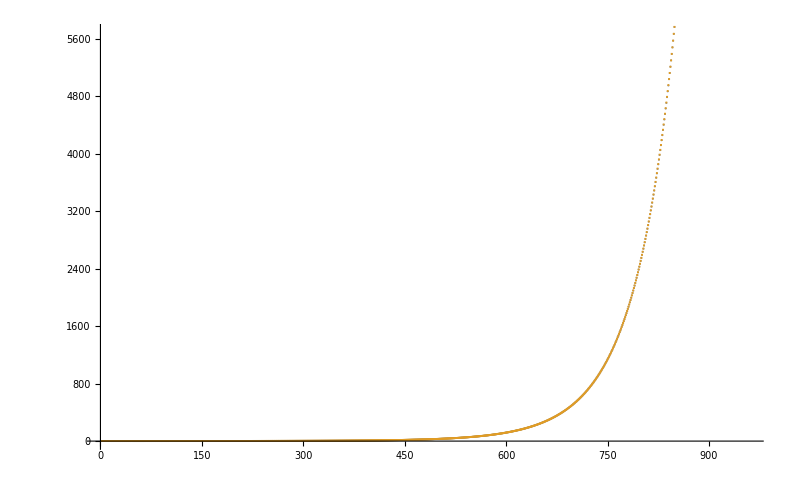

12763.2

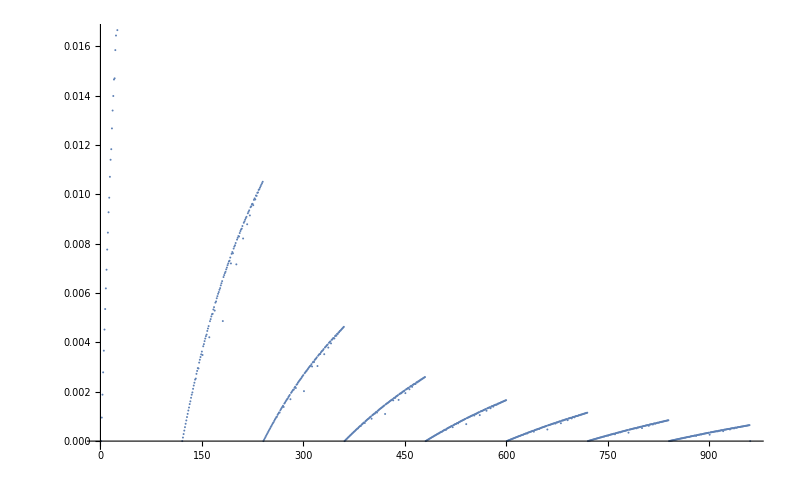

```mathematica
f[x_,dx_:1/1000000]:=Module[{p,a,b,q,r},
p=Rationalize[x,dx];
a=Numerator[p];
b=Denominator[p];
q=Quotient[a,b];
r=Mod[a,b];
Return[q!*Surd[Product[q+k/b+1/2-1/(2*b),{k,r}],b]]
]

x=Pi;

y=f[x];
z=x!;
N[y]
N[z]
N[Abs[y-z]]
1-N[y/z]

T=Table[{f[x],x!},{x,0,8,1/120}]ᵀ;
ListPlot[T,PlotMarkers->{Automatic, 2}]
N[Total[Map[(#[[1]]-#[[2]])^2&,Tᵀ]]]
ListPlot[Table[1-f[x]/x!,{x,0,8,1/120}],PlotMarkers->{Automatic, 2}]
```